```mathematica
DrawIsoLines [debit_ , coordinates_,xminlim_,xmaxlim_,yminlim_,ymaxlim_,phiCount_,psiCount_] := Module [
{we= debit,
coords = coordinates,
xminl=xminlim,
xmaxl=xmaxlim,
yminl=yminlim,
ymaxl=ymaxlim,
phiC=phiCount,
psiC=psiCount,
phi,psi,w,g1,g2},
w[z_]=0;
For[i=1,i<=Length[we],i++,w[z_]=w[z]+we[[i]]/(2π)*Log[z-(coords[[i,1]]+I*coords[[i,2]])]];
phi[z_]=Re[w[z]];
psi[z_]=Im[w[z]];
g1=ContourPlot[phi[x+I*y],{x,xminl,xmaxl},{y,yminl,ymaxl},PlotLegends->Automatic, Contours->phiC,ContourShading->None,AspectRatio->Automatic];
g2=ContourPlot[psi[x+I*y],{x,xminl,xmaxl},{y,yminl,ymaxl},PlotLegends->Automatic, Contours->psiC,ContourShading->None,AspectRatio->Automatic];
Show[g1,g2]];
```

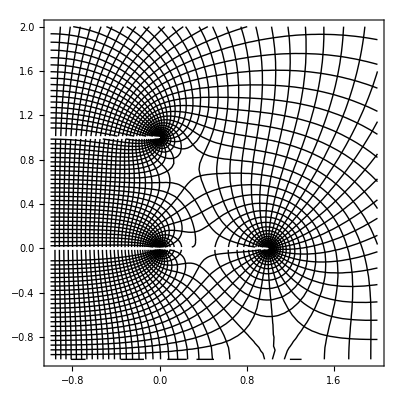

```mathematica
DrawIsoLines[{-1,-1,-1,
-1,-1,-1,
1,1,1,
1,1,1},
{{0,0},{1,0},{0,1},
{0,-2},{1,-2},{0,-3},
{-2,0},{-3,0},{-2,1},
{-2,-2},{-3,-2},{-2,-3}},-1,2,-1,2,40,70]
```

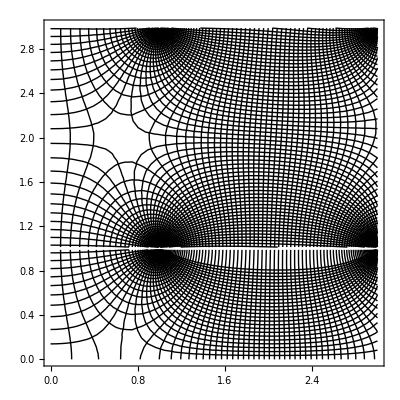

```mathematica
DrawIsoLines[{1,
1,
-1,-1,
1,1,-1,-1,
-1,-1,-1,-1,1,1,1,1},
{{1,1},
{1,3},
{3,1},{3,3},
{1,-1},{1,-3},{3,-1},{3,-3},
{-1,1},{-1,3},{-1,-1},{-1,-3},{-3,1},{-3,3},{-3,-1},{-3,-3}},
0,3,0,3,100,100]
```

```mathematica
PlotPhi[debit_ , coordinates_] := Module [
{we= debit,
coords = coordinates,

phi,psi,w,g1,g2},
w[z_]=0;
For[i=1,i<=Length[we],i++,w[z_]=w[z]+we[[i]]/(2π)*Log[z-(coords[[i,1]]+I*coords[[i,2]])]];
phi[z_]=Re[w[z]];
Plot[phi[2+I*y],{y,0,2}]
];
```

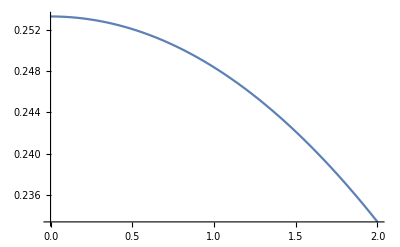

```mathematica
PlotPhi[{1,
1,
-1,-1,
1,1,-1,-1,
-1,-1,-1,-1,1,1,1,1},
{{1,1},
{1,3},
{3,1},{3,3},
{1,-1},{1,-3},{3,-1},{3,-3},
{-1,1},{-1,3},{-1,-1},{-1,-3},{-3,1},{-3,3},{-3,-1},{-3,-3}}]
```

```mathematica
(*Невозможно, потому что рекурсия*)
```